# 0) Preliminaries

```mathematica
plotFun[fun_,lims_,epilog_,label_,legs_:None]:=Framed@Plot[fun,{x,lims[[1,1]],lims[[1,2]]},PlotRange->{Full,{lims[[2,1]],lims[[2,2]]}},Epilog->epilog,PlotLegends->legs,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"x","y"},BaseStyle->{FontSize->20}]
```

```mathematica
discPlotFun[fun_,range_,lims_,epilog_,label_]:=Framed@DiscretePlot[fun,{n,range[[1]],range[[2]]},PlotRange->lims,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"M","y"},BaseStyle->{FontSize->20}]
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0}(*{(*maxran-20*)20,limit+.05}*),{(*maxran-25*)(*15*)ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos(*{(*maxran-20*)22,limit+.05}*),Left]},{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]},Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
(*ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
If[ilimpos===Automatic,ilimpos={22,limit+05}];
funplot=DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}];
epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}];
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" }
]
]*)
```

```mathematica
ClearAll[plotLimitDisc]
plotLimitDisc[fun_,n0fun_,epsran_,maxran_,limit_,label_,upreg_:True,lowreg_:True,seqname_:"a_n",epilog_:{},limpos_:Automatic]:=Module[{funplot,epsplot,ilimpos=limpos},
Manipulate[
Column[{
Show[funplot,epsplot[ϵ],epilog,PlotRange->{{0,maxran},All}],
Item[Style["ϵ = "<>ToString[ϵ],30],ItemSize->{All,4},Background->LightOrange]
},Frame->All],
{{ϵ,epsran[[2]]},epsran[[1]],epsran[[2]],Appearance->"Open" },
{{funplot,DiscretePlot[fun[n],{n,1,maxran},PlotRange->{Full,All},Filling->None,Epilog->epilog,PlotLabel->Style[label,Black,Bold,20],ImageSize->Large,AxesLabel->{"n","y"},BaseStyle->{FontSize->20}]},{0,1},ControlType->None},
{{ilimpos,If[limpos===Automatic,{22,limit+05},limpos]},ControlType->None},
SaveDefinitions->True,Initialization:>{epsplot[ϵ_]:=Graphics[{
(*limit line and label*)
{Line[{{1,limit},{maxran,limit}}],Arrow[{ilimpos-{0.5,0},{ilimpos[[1]]-5,limit}}],Text["lim_(n → ∞) "<>seqname<>"="<>ToString[limit],ilimpos,Left]},

(*lower region*)
If[upreg,{{Thick,Orange,Line[{{0,limit-ϵ},{maxran,limit-ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit-ϵ}}],Text[Style["ϵ",20],{4,limit-ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit-ϵ},{maxran,limit}]}},{}],

(*upper region*)
If[lowreg,{{Thick,Orange,Line[{{0,limit+ϵ},{maxran,limit+ϵ}}]},{Arrowheads[{-.03,.03}],Arrow[{{5,limit},{5,limit+ϵ}}],Text[Style["ϵ",20],{4,limit+ϵ/2}]},{Opacity[.5],Orange,Rectangle[{0,limit+ϵ},{maxran,limit}]}},{}],

(*moving n0*)
Module[{n0=n0fun[ϵ]},{Line[{{n0,fun[n0]},{n0,0}}],Text[Style["n_0= "<>ToString[n0fun[ϵ]],20],{n0+1.5,.05},Left]}]
}]}
]
]
```

# 1) Reihen

a) ∑_(n=1)^∞ (-1)^n/(√n)

b) ∑_(n=1)^∞ n/(2n+1)^3

c) ∑_(n=1)^∞ (n+1)/2^n

#### Useful formulas

Leibnitz Kriterium

a_n↘ 0    ⇒   ∑_(n=1)^∞ (-1)^n a_n konvergent

Majorantenkriterium

∑_(n=1)^∞ b_n konvergent, b_n≥0, Abs[a_n]≤b_n   ⇒   ∑_(n=1)^∞ a_n absolut konvergent

Quotientenkriterium I

∀n≥n_0: a_n≠0  ∧  Abs[a_(n+1)]/Abs[a_n]≤θ, 0<θ<1  ⇒   ∑_(n=1)^∞ a_n absolut konvergent

Quotientenkriterium II

a_n≠0, lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=θ  ⇒
θ<1:   ∑_(n=1)^∞ a_n absolut konvergent
θ>1:   ∑_(n=1)^∞ a_n divergent

## Plots

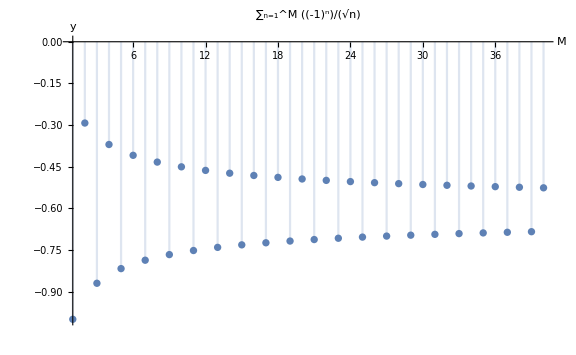

```mathematica
discPlotFun[∑_(k=1)^n (-1)^k/(√k),{1,40},{{1,40},All},{},"∑_(n=1)^M (-1)^n/(√n)"]
```

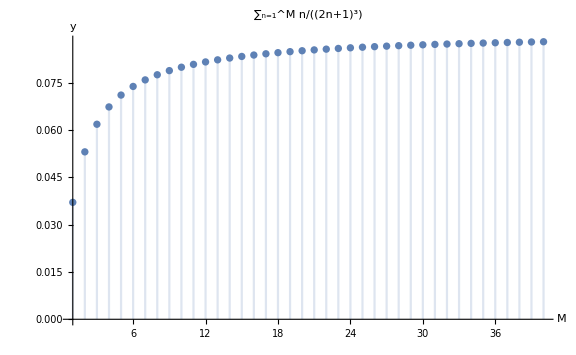

```mathematica
discPlotFun[∑_(k=1)^n k/(2k+1)^3,{1,40},{{1,40},All},{},"∑_(n=1)^M n/(2n+1)^3"]
```

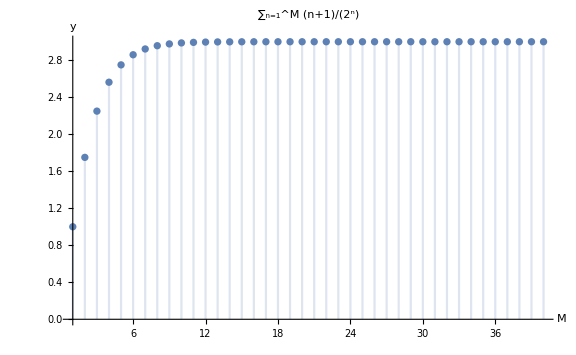

```mathematica
discPlotFun[∑_(k=1)^n (k+1)/2^k,{1,40},{{1,40},All},{},"∑_(n=1)^M (n+1)/2^n"]
```

## Solution

## a)

Leibnitz Kriterium:

a_n:=1/(√n)

It holds that a_n≥0, monotonically decreasing, and lim_(n→∞) a_n=0.

Therefore convergent.

## b)

Majorantenkriterium:

a_n:=n/(2n+1)^3

n/(2n+1)^3≤(2n+1)/(2n+1)^3=1/((2n+1)(2n+1))≤1/((n+1)(n+1))≤1/(n(n+1))

We know that ∑_(n=1)^∞ 1/(n(n+1)) converges (see the beginning of page 44 in Skriptum), so ∑_(n=1)^∞ n/(2n+1)^3also converges.

## c)

Quotientenkriterium:

a_n:=(n+1)/2^n

It holds that a_n>0 and lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) ((n+2)/2^(n+1))/((n+1)/2^n)=lim_(n→∞) 1/2(n+2)/(n+1)=1/2=θ.

As θ<1, the Reihe converges.

# 2) Reihe mit Parameter

∑_(n=1)^∞ x^(3n)/((2n)!)

For which x∈ℝ convergent?

## Plot

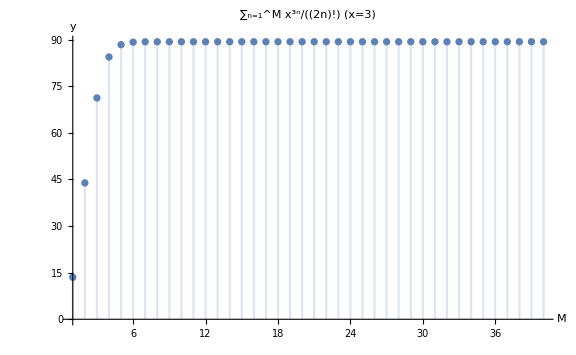

```mathematica
discPlotFun[With[{x=3.},∑_(k=1)^n x^(3k)/((2k)!)],{1,40},{{1,40},All},{},"∑_(n=1)^M x^(3n)/((2n)!)  (x=3)"]
```

## Solution

Quotientenkriterium:

a_n:=x^(3n)/((2n)!)

It holds that a_n≠0 (whenever x≠0) and lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) Abs[x^(3n+3)/((2n+2)!)]/Abs[x^(3n)/((2n)!)]=Abs[x^3]·lim_(n→∞) ((2n)!)/((2n+2)!)=Abs[x^3]·lim_(n→∞) 1/((2n+2)(2n+1))=Abs[x^3]·lim_(n→∞) 1/((2+2/n)(2+1/n))1/n^2=0=θ

As θ<1 the Reihe converges for all x∈ℝ.

# 3) Divergente Reihe

∑_(n=1)^∞ 1/(√n)

Divergent?

## Solution

Compare with the harmonische Reihe ∑_(n=1)^∞ 1/n.

n^2≥n ⇒n≥√n ⇒1/(√n)≥1/n

Thence:  ∑_(n=1)^M 1/(√n)≥∑_(n=1)^M 1/n  for all M∈ℕ.

Since lim_(M→∞) ∑_(n=1)^M 1/n=∞ we get lim_(M→∞) ∑_(n=1)^M 1/(√n)=∞ and the Reihe diverges.

# 4) Logarithmus

ln(1+x)=∑_(n=1)^∞ (-1)^(n+1)/n x^n=x-x^2/2+x^3/3-...

For which x∈ℝ converges (absolutely)? What happens for x=±1?

## Solution

Quotientenkriterium:

lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) Abs[(-1)^(n+2)/(n+1)x^(n+1)]/Abs[(-1)^(n+1)/n x^n]=Abs[x]·lim_(n→∞) n/(n+1)=Abs[x]

So for Abs[x]<1 converges absolutely, for Abs[x]>1 diverges.

For x=1 we get:  ∑_(n=1)^∞ (-1)^(n+1)/n 1^n=-∑_(n=1)^∞ (-1)^n 1/n. Using the Leibnitz Kriterium, where a_n:=1/n, we can easily see that the Reihe converges. The Reihe does not converge absolutely though, as  ∑_(n=1)^∞ Abs[((-1)^(n+1) 1^n)/n]=∑_(n=1)^∞ 1/n. It is the harmonische Reihe, which diverges.

For x=-1 we get:  ∑_(n=1)^∞ (-1)^(n+1)/n(-1)^n=-∑_(n=1)^∞ 1/n, i.e. the harmonische Reihe, which diverges.

To conclude:

-∞<x≤-1: divergent
-1<x<1: absolutely convergent
x=1: convergent (not absolutely)
1<x<∞: divergent

# 5) Cauchy-Produkt

1/(1-x)=∑_(n=0)^∞ x^n

a) (∑_(n=0)^∞ x^n) · (∑_(n=0)^∞ x^n) = ?

b) For which x∈ℝ convergent?

#### Useful formulas

Cauchy-Produkt

A=∑_(n=0)^∞ a_n,   B=∑_(n=0)^∞ b_n :

A·B = ∑_(n=0)^∞ c_n,    where    c_n=∑_(k=0)^n a_k b_(n-k)

## Solution

## a)

A=B=∑_(n=0)^∞ x^n:  A·B = ∑_(n=0)^∞ c_n, where c_n=∑_(k=0)^n x^k x^(n-k) and so:

c_n=∑_(k=0)^n x^k x^(n-k)=∑_(k=0)^n x^n=(n+1)x^n

Therefore: 1/(1-x)·1/(1-x)=1/(1-x)^2=∑_(n=0)^∞ (n+1)x^n.

## b)

Quotientenkriterium:

a_n:=(n+1)x^n

lim_(n→∞) Abs[a_(n+1)]/Abs[a_n]=lim_(n→∞) Abs[(n+2)x^(n+1)]/Abs[(n+1)x^n]=Abs[x]·lim_(n→∞) (n+2)/(n+1)=Abs[x]

Thus for Abs[x]<1 converges absolutely, for Abs[x]>1 diverges, i.e. the Konvergenzradius is 1. For x=1 we get ∑_(n=0)^∞ (n+1), which diverges, and for x=-1 we get ∑_(n=0)^∞ (n+1)(-1)^n, which also diverges.